```mathematica
<<basisConversion.m
```

```mathematica
<<HPL.m
```

*-*-*-*-*-* HPL 2.0 *-*-*-*-*-*

Author: Daniel Maitre, University of Zurich

Rules for minimal set loaded for weights: 2, 3, 4, 5, 6.

Rules for minimal set for + - weights loaded for weights: 2, 3, 4, 5, 6.

Table of MZVs loaded up to weight 6

Table of values at I loaded up to weight 6

$HPLFunctions gives a list of the functions of the package.
$HPLOptions gives a list of the options of the package.

More info in hep-ph/0507152, hep-ph/0703052 and at 
 http://krone.physik.unizh.ch/~maitreda/HPL/

```mathematica
c43u0:=-1/48*(ln[w]*(H4m[u]+2*H31m[u]+H211m[u]-H2m[u]^2)-4*H5m[u]-4*H41m[u]-2*H32m[u]+4*H311m[u]+2*H221m[u]+4*H2111m[u]+2*H2m[u]*H3m[u]-2*H2m[u]*H21m[u]-ln[u]*(-H4m[u]-2*H31m[u]-H211m[u]+H2m[u]^2));
```

```mathematica
c42u0:=1/32*(ln[w]^2*(-3*H4m[u]+7*H31m[u]-5*H211m[u]+7/2*H2m[u]^2-ln[u]*(H3m[u]-H21m[u]))+ln[w]*(32*H5m[u]-30*H41m[u]+2*H32m[u]+54*H311m[u]+6*H221m[u]-36*H2111m[u]-22*H2m[u]*H3m[u]+18*H2m[u]*H21m[u]-ln[u]*(6*H4m[u]-8*H31m[u]+6*H211m[u]-8*H2m[u]^2-ln[u]*(H21m[u]-H3m[u]))+12*Zeta[2]*(H3m[u]-H21m[u]))-100*H6m[u]+76*H51m[u]-6*H42m[u]-36*H411m[u]+18*H321m[u]+4*H312m[u]+92*H3111m[u]+2*H2211m[u]-80*H21111m[u]+H2m[u]*(18*H4m[u]-24*H31m[u]+10*H211m[u]+1/3*H2m[u]^2)+H3m[u]*(16*H3m[u]-34*H21m[u])+18*H21m[u]^2-ln[u]*(-44*H5m[u]+30*H41m[u]-4*H32m[u]-46*H311m[u]-4*H221m[u]+32*H2111m[u]+24*H2m[u]*H3m[u]-20*H2m[u]*H21m[u]-ln[u]*(-6*H4m[u]+5*H31m[u]-4*H211m[u]+9/2*H2m[u]^2))+Zeta[2]*(-30*H4m[u]+46*H31m[u]-34*H211m[u]-H2m[u]^2+10*ln[u]*(H3m[u]-H21m[u]))+8*Zeta[3]*(2*H3m[u]-H21m[u]-ln[u]*H2m[u]));
```

```mathematica
c41u0:=1/16*(ln[w]^3*(-H4m[u]+2/3*H31m[u]-1/3*H211m[u]+H2m[u]^2-1/6*ln[u]*(8*H3m[u]-10*H21m[u]+ln[u]*H2m[u]))+ln[w]^2*(24*H5m[u]-23*H41m[u]+H32m[u]+9*H311m[u]-5*H221m[u]-28*H2111m[u]-17*H2m[u]*H3m[u]+18*H2m[u]*H21m[u]-ln[u]*(-5*H4m[u]+3*H31m[u]-3*H211m[u]-9/2*H2m[u]^2-ln[u]*(-3*H3m[u]+3*H21m[u]-1/6*ln[u]*H2m[u]))+6*Zeta[2]*(2*H3m[u]-3*H21m[u]+ln[u]*H2m[u]))+ln[w]*(-200*H6m[u]+172*H51m[u]-4*H42m[u]-192*H411m[u]-4*H321m[u]+168*H3111m[u]-4*H2211m[u]-200*H21111m[u]+H2m[u]*(60*H4m[u]-44*H31m[u]+54*H211m[u]-19/3*H2m[u]^2)+H3m[u]*(25*H3m[u]-48*H21m[u])+21*H21m[u]^2-ln[u]*(-56*H5m[u]+52*H41m[u]-2*H32m[u]-54*H311m[u]+2*H221m[u]+60*H2111m[u]+48*H2m[u]*H3m[u]-44*H2m[u]*H21m[u]-ln[u]*(2*H4m[u]+H31m[u]+15/2*H2m[u]^2-ln[u]*(2*H3m[u]-5/3*H21m[u])))+Zeta[2]*(-80*H4m[u]+64*H31m[u]-76*H211m[u]+20*H2m[u]^2-ln[u]*(-12*H3m[u]+10*H21m[u]-5*ln[u]*H2m[u]))+Zeta[3]*(4*H3m[u]+2/3*ln[u]^3)-108*Zeta[4]*H2m[u])+600*H7m[u]-420*H61m[u]+40*H52m[u]+536*H511m[u]+10*H43m[u]+50*H421m[u]+18*H412m[u]+36*H4111m[u]+22*H331m[u]+8*H322m[u]+156*H3211m[u]+74*H3121m[u]+70*H3112m[u]+320*H31111m[u]-24*H2221m[u]-400*H211111m[u]-44*H22111m[u]-14*H21211m[u]+H3m[u]*(-66*H4m[u]+50*H31m[u]-48*H211m[u])+H21m[u]*(64*H4m[u]-46*H31m[u]+58*H211m[u])+H2m[u]*(-84*H5m[u]+62*H41m[u]-4*H32m[u]-98*H311m[u]+12*H221m[u]+60*H2111m[u]+13*H2m[u]*H3m[u]-15*H2m[u]*H21m[u])-ln[u]*(320*H6m[u]-260*H51m[u]+6*H42m[u]+270*H411m[u]+6*H321m[u]-4*H312m[u]-232*H3111m[u]-2*H2211m[u]+200*H21111m[u]+H3m[u]*(-38*H3m[u]+70*H21m[u])-36*H21m[u]^2+H2m[u]*(-74*H4m[u]+58*H31m[u]-54*H211m[u]+20/3*H2m[u]^2)-ln[u]*(68*H5m[u]-60*H41m[u]+62*H311m[u]+4*H221m[u]-40*H2111m[u]-34*H2m[u]*H3m[u]+29*H2m[u]*H21m[u]-ln[u]*(6*H4m[u]-6*H31m[u]+10/3*H211m[u]-4*H2m[u]^2)))+Zeta[2]*(152*H5m[u]-122*H41m[u]+6*H32m[u]+82*H311m[u]-14*H221m[u]-136*H2111m[u]-30*H2m[u]*H3m[u]+36*H2m[u]*H21m[u]-ln[u]*(64*H4m[u]-46*H31m[u]+56*H211m[u]-15*H2m[u]^2-ln[u]*(10*H3m[u]-8*H21m[u]-1/3*ln[u]*H2m[u])))+Zeta[3]*(-52*H4m[u]+28*H31m[u]-20*H211m[u]+6*H2m[u]^2-ln[u]*(-28*H3m[u]+24*H21m[u]+6*ln[u]*H2m[u]))+Zeta[4]*(152*H3m[u]-184*H21m[u]-76*ln[u]*H2m[u])-(40*Zeta[5]+8*Zeta[2]*Zeta[3])*(H2m[u]+1/2*ln[u]^2));
```

```mathematica
c40u0:=1/32*(ln[w]^4*(-1/6*H4m[u]-7/6*H31m[u]+1/2*H211m[u]+1/6*H2m[u]^2-ln[u]*(1/2*H3m[u]+1/6*H21m[u]+1/4*ln[u]*H2m[u]-1/144*ln[u]^3))+ln[w]^3*(32/3*H5m[u]-2*H41m[u]-4/3*H32m[u]+16/3*H311m[u]+4/3*H221m[u]+10/3*H2111m[u]-14/3*H2m[u]*H3m[u]+8/3*H2m[u]*H21m[u]-ln[u]*(-10*H4m[u]+28/3*H31m[u]-34/3*H211m[u]-2/3*H2m[u]^2-ln[u]*(-2*H3m[u]+7/3*H21m[u]-5/9*ln[u]*H2m[u]))+Zeta[2]*(4*H3m[u]+8*H21m[u]+8*ln[u]*H2m[u]-2/3*ln[u]^3))+ln[w]^2*(-200*H6m[u]+136*H51m[u]+2*H42m[u]-114*H411m[u]+2*H321m[u]-4*H312m[u]+110*H3111m[u]-6*H2211m[u]-160*H21111m[u]+H3m[u]*(32*H3m[u]-64*H21m[u])+26*H21m[u]^2+H2m[u]*(36*H4m[u]-28*H31m[u]+32*H211m[u]-5/3*H2m[u]^2)-ln[u]*(16*H5m[u]-26*H41m[u]-6*H32m[u]+30*H311m[u]+6*H221m[u]-8*H2111m[u]+34*H2m[u]*H3m[u]-32*H2m[u]*H21m[u]-ln[u]*(29*H4m[u]-27*H31m[u]+26*H211m[u]+4*H2m[u]^2-ln[u]*(13/3*H3m[u]-14/3*H21m[u]+1/3*ln[u]*H2m[u])))+Zeta[2]*(-80*H4m[u]+48*H31m[u]-60*H211m[u]+9*H2m[u]^2-ln[u]*(24*H3m[u]-8*H21m[u]-9*ln[u]*H2m[u]-1/12*ln[u]^3))+8*Zeta[3]*(H3m[u]+H21m[u])-54*Zeta[4]*(2*H2m[u]-ln[u]^2))+ln[w]*(1600*H7m[u]-1120*H61m[u]+40*H52m[u]+856*H511m[u]+12*H43m[u]-124*H421m[u]-36*H412m[u]-1916*H4111m[u]-44*H331m[u]-16*H322m[u]-288*H3211m[u]-148*H3121m[u]-140*H3112m[u]+1080*H31111m[u]+48*H2221m[u]-32*H22111m[u]-4*H21211m[u]-1400*H211111m[u]+H3m[u]*(-176*H4m[u]+160*H31m[u]-168*H211m[u])+H21m[u]*(168*H4m[u]-152*H31m[u]+128*H211m[u])+H2m[u]*(-208*H5m[u]+168*H41m[u]+8*H32m[u]-80*H311m[u]-24*H221m[u]+184*H2111m[u]+30*H2m[u]*H3m[u]-22*H2m[u]*H21m[u])-ln[u]*(560*H6m[u]-424*H51m[u]+16*H42m[u]+320*H411m[u]-48*H321m[u]-424*H3111m[u]+16*H2211m[u]+560*H21111m[u]+H3m[u]*(-106*H3m[u]+208*H21m[u])-82*H21m[u]^2+H2m[u]*(-152*H4m[u]+132*H31m[u]-140*H211m[u]+32/3*H2m[u]^2)-ln[u]*(28*H5m[u]-10*H41m[u]+10*H32m[u]+16*H311m[u]-10*H221m[u]-56*H2111m[u]-74*H2m[u]*H3m[u]+68*H2m[u]*H21m[u]-ln[u]*(-50/3*H4m[u]+40/3*H31m[u]-28/3*H211m[u]-22/3*H2m[u]^2-ln[u]*(-3*H3m[u]+7/3*H21m[u]))))+Zeta[2]*(416*H5m[u]-288*H41m[u]-4*H32m[u]+364*H311m[u]+20*H221m[u]-292*H2111m[u]-72*H2m[u]*H3m[u]+44*H2m[u]*H21m[u]-ln[u]*(72*H4m[u]-80*H31m[u]+64*H211m[u]-12*H2m[u]^2-ln[u]*(-14*H3m[u]+12*H21m[u]+14/3*ln[u]*H2m[u])))+Zeta[3]*(-72*H4m[u]+8*H31m[u]+72*H211m[u]+4*H2m[u]^2+8*ln[u]*H3m[u])+Zeta[4]*(488*H3m[u]-208*H21m[u]+32*ln[u]*H2m[u]-12*ln[u]^3)-(876*Zeta[6]+32*Zeta[3]^2)*ln[u])-4900*H8m[u]+3460*H71m[u]-120*H62m[u]-4900*H611m[u]-32*H53m[u]-648*H521m[u]-48*H512m[u]+3620*H5111m[u]-144*H431m[u]+64*H422m[u]+408*H4211m[u]-80*H413m[u]+144*H4121m[u]-1400*H41111m[u]+48*H332m[u]+144*H3311m[u]+48*H3221m[u]+440*H32111m[u]+208*H31211m[u]+176*H31121m[u]+112*H31112m[u]+2440*H311111m[u]-48*H22211m[u]-16*H22121m[u]-120*H221111m[u]-32*H212111m[u]-2800*H2111111m[u]+210*H4m[u]^2+162*H31m[u]^2+154*H211m[u]^2-384*H4m[u]*H31m[u]+384*H4m[u]*H211m[u]-336*H31m[u]*H211m[u]+H3m[u]*(32*H5m[u]+28*H41m[u]-24*H32m[u]-24*H311m[u]-8*H221m[u]-8*H2111m[u])+H21m[u]*(-8*H5m[u]-16*H41m[u]-8*H32m[u]+28*H311m[u]+8*H221m[u]+8*H2111m[u])+H2m[u]*(600*H6m[u]-456*H51m[u]+348*H411m[u]-16*H321m[u]-512*H3111m[u]+440*H21111m[u]+H2m[u]*(-90*H4m[u]+82*H31m[u]-70*H211m[u]+23/6*H2m[u]^2)+H3m[u]*(6*H3m[u]+4*H21m[u])-2*H21m[u]^2)-ln[u]*(-2900*H7m[u]+1940*H61m[u]-160*H52m[u]-2300*H511m[u]-44*H43m[u]-204*H421m[u]-76*H412m[u]+1672*H4111m[u]-84*H331m[u]-32*H322m[u]-40*H3211m[u]-12*H3121m[u]-4*H3112m[u]-1600*H31111m[u]+24*H22111m[u]+4*H21211m[u]+1600*H211111m[u]+H3m[u]*(292*H4m[u]-228*H31m[u]+232*H211m[u])+H21m[u]*(-256*H4m[u]+220*H31m[u]-204*H211m[u])+H2m[u]*(360*H5m[u]-252*H41m[u]+16*H32m[u]+260*H311m[u]-272*H2111m[u]-56*H2m[u]*H3m[u]+48*H2m[u]*H21m[u])-ln[u]*(-750*H6m[u]+582*H51m[u]-10*H42m[u]-510*H411m[u]+6*H321m[u]+4*H312m[u]+452*H3111m[u]-2*H2211m[u]-400*H21111m[u]+H3m[u]*(85*H3m[u]-152*H21m[u])+67*H21m[u]^2+H2m[u]*(152*H4m[u]-126*H31m[u]+120*H211m[u]-37/3*H2m[u]^2)-ln[u]*(-310/3*H5m[u]+256/3*H41m[u]-212/3*H311m[u]+160/3*H2111m[u]+142/3*H2m[u]*H3m[u]-124/3*H2m[u]*H21m[u]-ln[u]*(-20/3*H4m[u]+17/3*H31m[u]-10/3*H211m[u]+25/6*H2m[u]^2))))+Zeta[2]*(-600*H6m[u]+424*H51m[u]-8*H42m[u]-300*H411m[u]+40*H321m[u]+404*H3111m[u]-8*H2211m[u]-480*H21111m[u]-20*H3m[u]*H21m[u]+8*H21m[u]^2+H2m[u]*(108*H4m[u]-104*H31m[u]+84*H211m[u]-8/3*H2m[u]^2)-ln[u]*(-200*H5m[u]+128*H41m[u]-20*H32m[u]-152*H311m[u]+4*H221m[u]+192*H2111m[u]+52*H2m[u]*H3m[u]-48*H2m[u]*H21m[u]-ln[u]*(-26*H4m[u]+20*H31m[u]-28*H211m[u]+9*H2m[u]^2-ln[u]*(-10/3*H3m[u]+8/3*H21m[u]+2/3*ln[u]*H2m[u]))))+Zeta[3]*(320*H5m[u]-208*H41m[u]-32*H32m[u]-48*H311m[u]-32*H221m[u]+80*H2111m[u]-32*H2m[u]*H3m[u]+8*H2m[u]*H21m[u]-ln[u]*(152*H4m[u]-72*H31m[u]+24*H211m[u]-12*H2m[u]^2-ln[u]*(28*H3m[u]-20*H21m[u]-8/3*ln[u]*H2m[u])))+Zeta[4]*(-565*H4m[u]+509*H31m[u]-541*H211m[u]+34*H2m[u]^2-ln[u]*(-121*H3m[u]+217*H21m[u]+65/2*ln[u]*H2m[u]-7/24*ln[u]^3))+(80*Zeta[5]+16*Zeta[2]*Zeta[3])*(3*H3m[u]-ln[u]*H2m[u])-(219*Zeta[6]+8*Zeta[3]^2)*(2*H2m[u]-ln[u]^2));
```

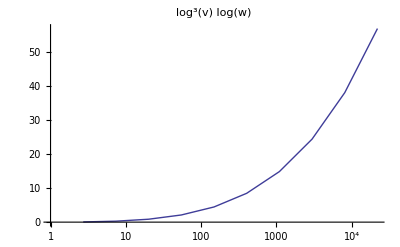

```mathematica
ListLogLinearPlot[Coefficient[Expand[c43u0/.convertLanceToMe],Log[w],1]/.{u->Exp[#]}&/@Range[10],Joined->True,AxesOrigin->{1,0},PlotLabel->Style[Text[Log[v]^3 * Log[w]],FontSize->18]]
```

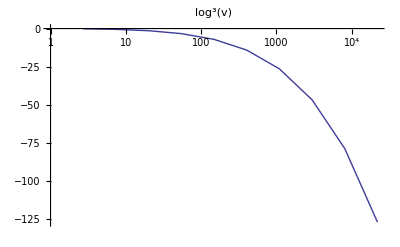

```mathematica
ListLogLinearPlot[Coefficient[Expand[c43u0/.convertLanceToMe],Log[w],0]/.{u->Exp[#]}&/@Range[10],Joined->True,AxesOrigin->{1,0},PlotLabel->Style[Text[Log[v]^3],FontSize->18]]
```

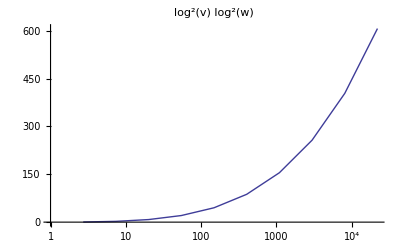

```mathematica
ListLogLinearPlot[Coefficient[Expand[c42u0/.convertLanceToMe],Log[w],2]/.{u->Exp[#]}&/@Range[10],Joined->True,AxesOrigin->{1,0},PlotLabel->Style[Text[Log[v]^2 * Log[w]^2],FontSize->18]]
```

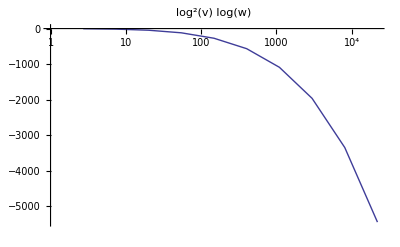

```mathematica
ListLogLinearPlot[Coefficient[Expand[c42u0/.convertLanceToMe],Log[w],1]/.{u->Exp[#]}&/@Range[10],Joined->True,AxesOrigin->{1,0},PlotLabel->Style[Text[Log[v]^2 * Log[w]],FontSize->18]]
```

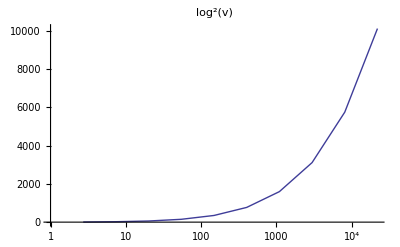

```mathematica
ListLogLinearPlot[Coefficient[Expand[c42u0/.convertLanceToMe],Log[w],0]/.{u->Exp[#]}&/@Range[10],Joined->True,AxesOrigin->{1,0},PlotLabel->Style[Text[Log[v]^2],FontSize->18]]
```

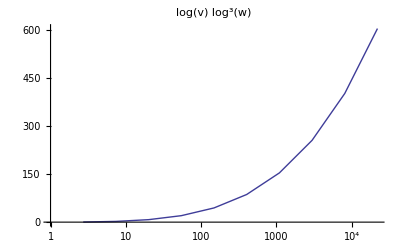

```mathematica
ListLogLinearPlot[Coefficient[Expand[c41u0/.convertLanceToMe],Log[w],3]/.{u->Exp[#]}&/@Range[10],Joined->True,AxesOrigin->{1,0},PlotLabel->Style[Text[Log[v] * Log[w]^3],FontSize->18]]
```

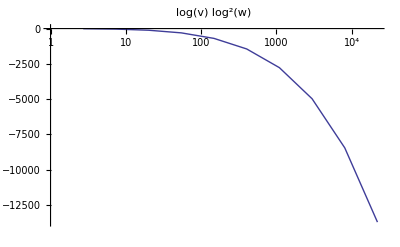

```mathematica
ListLogLinearPlot[Coefficient[Expand[c41u0/.convertLanceToMe],Log[w],2]/.{u->Exp[#]}&/@Range[10],Joined->True,AxesOrigin->{1,0},PlotLabel->Style[Text[Log[v] * Log[w]^2],FontSize->18]]
```

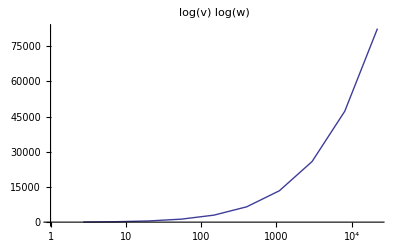

```mathematica
ListLogLinearPlot[Coefficient[Expand[c41u0/.convertLanceToMe],Log[w],1]/.{u->Exp[#]}&/@Range[10],Joined->True,AxesOrigin->{1,0},PlotLabel->Style[Text[Log[v] * Log[w]],FontSize->18]]
```

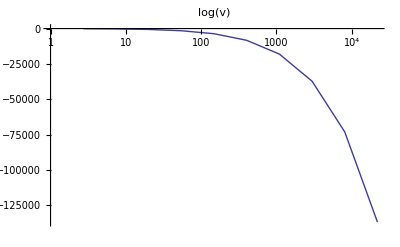

```mathematica
ListLogLinearPlot[Coefficient[Expand[c41u0/.convertLanceToMe],Log[w],0]/.{u->Exp[#]}&/@Range[10],Joined->True,AxesOrigin->{1,0},PlotLabel->Style[Text[Log[v] ],FontSize->18]]
```

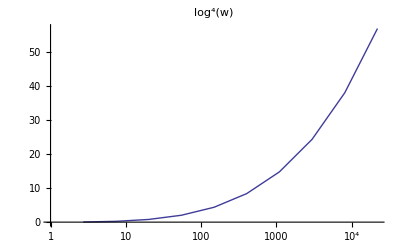

```mathematica
ListLogLinearPlot[Coefficient[Expand[c40u0/.convertLanceToMe],Log[w],4]/.{u->Exp[#]}&/@Range[10],Joined->True,AxesOrigin->{1,0},PlotLabel->Style[Text[Log[w]^4 ],FontSize->18]]
```

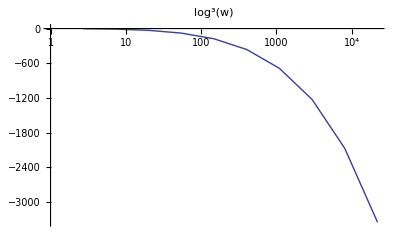

```mathematica
ListLogLinearPlot[Coefficient[Expand[c40u0/.convertLanceToMe],Log[w],3]/.{u->Exp[#]}&/@Range[10],Joined->True,AxesOrigin->{1,0},PlotLabel->Style[Text[Log[w]^3],FontSize->18]]
```

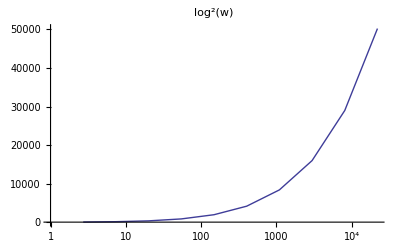

```mathematica
ListLogLinearPlot[Coefficient[Expand[c40u0/.convertLanceToMe],Log[w],2]/.{u->Exp[#]}&/@Range[10],Joined->True,AxesOrigin->{1,0},PlotLabel->Style[Text[Log[w]^2],FontSize->18]]
```

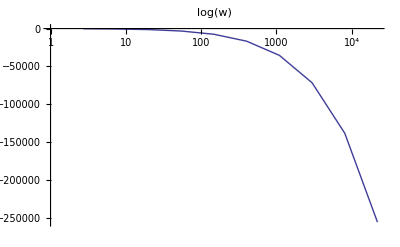

```mathematica
ListLogLinearPlot[Coefficient[Expand[c40u0/.convertLanceToMe],Log[w],1]/.{u->Exp[#]}&/@Range[10],Joined->True,AxesOrigin->{1,0},PlotLabel->Style[Text[Log[w] ],FontSize->18]]
```

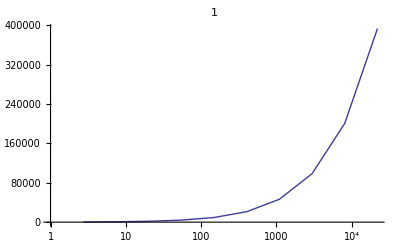

```mathematica
ListLogLinearPlot[Coefficient[Expand[c40u0/.convertLanceToMe],Log[w],0]/.{u->Exp[#]}&/@Range[10],Joined->True,AxesOrigin->{1,0},PlotLabel->Style[Text[1],FontSize->18]]
```